```mathematica
(***************************************)
(****Scalar field equaition*************)
(***************************************)
scfII[k_]:=pi''[t]-3 H[t] (1-w/cs^2)Ψ[k]+3 H[t]^2 cs^2 pi[t]+3H[t]w pi[t]+3 cs^2 Φ'[t]+Ψ'[t]+k^2 pi[t];
(*Matter dominated*)
Ψ'[t]=0;Φ'[t]=0;
(*Changing t->a*)
scfI[k_]:=scfII[k]/.pi->(pi[a[#]]&);
(**********************)
(**Matter Dominated era*)
(**********************)
(*Matter dominated, a-> t^(2/3)*)
H[t]=2/(3 a^(3/2));H'[t]=(-a'[t])/a^(5/2);
a''[t]=a[t](H[t]^2+H'[t]);
a'[t]=a[t]H[t];
(*Field equation in terms of scale factor!*)
scf[k_]:=scfI[k]/.a[t]:>a;
(***************************************)
(***************IC read fromt he file***)
(***************************************)
```

0.000549948+0.710308 10^(-12 x)-0.20009 ⅇ^(-20 x)+0.0957077 ⅇ^(-5 x)-0.0000213028 x+1.96231×10^-7 x^2-5.00079×10^-10 x^3

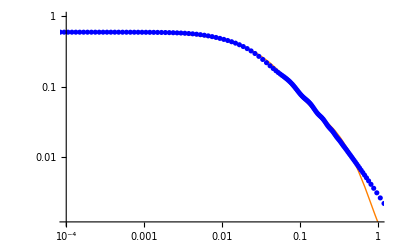

```mathematica
data=Import["/Users/farbod/Packages/Mathematica/Scalar_field_solving!/Class_kess_cs_e3_z100_newt_Gev.dat",{"Data",{All},{1,6}}];

ListLogLogPlot[data[[All,{1,2}]]];


FitΨ=Fit[data[[All,{1,2}]],{1,x,x^2,x^3,E^(-20x),E^(-5x),10^(-12x)},x]

p1=LogLogPlot[FitΨ,{x,0.0001,1},PlotStyle->{Orange,Line,Thick}];
p2=ListLogLogPlot[data[[All,{1,2}]],PlotStyle->{Blue,Dashed,Thick}];
Show[p1,p2]
```

```mathematica
(***************************************)
(***************IC Done!****************)
(***************************************)
```

```mathematica
scf[k]
```

(4 cs^2 pi[a])/(3 a^3)+k^2 pi[a]+(2 w pi[a])/a^(3/2)-(2 (1-w/cs^2) Ψ[k])/a^(3/2)-(2 pi'[a])/(9 a^2)+(4 pi''[a])/(9 a)

```mathematica
(*According to Poisson eq*)
(*k^2 Ψ[k]=δ -> Ψ[k]=Ak^(ns-3), used for fitting function*)
cs=10^-3;w=-0.9;
Ψfit[x_]:=0.0005499483196576216+0.7103084943795099 10^(-12 x)-0.20009029784996626 ⅇ^(-20 x)+0.0957076949121351 ⅇ^(-5 x)-0.000021302820000956537 x+1.9623061920169657*^-7 x^2-5.000787681656844*^-10 x^3;
Ψ[k]=Ψfit[k]
pi0[k_]:=555 Ψ[k];
piv0[k_]:=0.31 Ψ[k];
a0=1./(1.+100.);
a1=1./(1.+20.);
```

0.000549948+0.710308 10^(-12 k)-0.20009 ⅇ^(-20 k)+0.0957077 ⅇ^(-5 k)-0.0000213028 k+1.96231×10^-7 k^2-5.00079×10^-10 k^3

```mathematica
Sol=ParametricNDSolve[{scf[k]==0,pi[a0]==150,pi'[a0]==0.1},{pi},{a,a0,a1},{k}]
```

{pi→ParametricFunction[<>]}

```mathematica
dataPi=Import["/Users/farbod/Packages/Mathematica/Scalar_field_solving!/Class_kess_cs_e3_z100_newt_Gev.dat",{"Data",{All},{1,2}}];
```

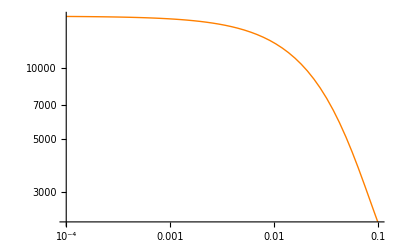

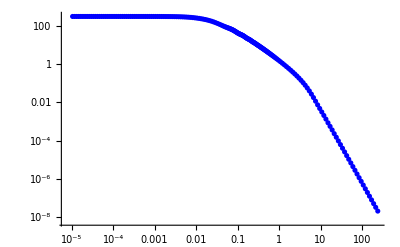

-Graphics-

```mathematica
p11=LogLogPlot[Evaluate[pi[k][a1]/.Sol],{k,0.0001,0.1},PlotStyle->{Orange,Line,Thick}];
p22=ListLogLogPlot[dataPi[[All,{1,2}]],PlotStyle->{Blue,Line,Thick}];
Show[p11]
Show[p22]
Show[p11,p22]
```